# 1. Bisection Method

Find the solution of equation using Bisection Method
Function :

```mathematica
bisection[f_,ao_,bo_,n_] := Module[{},a = N[ao];
b=N[bo];
If [f[a]*f[b]>0,
Print["Bisection Method can not be applied !!"]
Return[]];
p=(a+b)/2;
i=1;
While[i≤n,
If [f[a]*f[p]<0, b=p, a=p];
Print[i,"       ", a, "         ",b];
i++;
p=(a+b)/2];
Print["Root  = ",p];
Plot[f[x],{x,-3,3},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed],PlotStyle->{Thickness[0.004],Blue},PlotLegends->{f[x]},Frame->True]
]
```

## Question -1

```mathematica
f[x_] := x^3 +x^2-3*x-3
```

1       1.5         2.

2       1.5         1.75

3       1.625         1.75

4       1.6875         1.75

5       1.71875         1.75

Root  = 1.73438

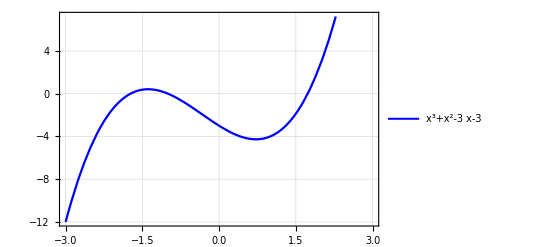

```mathematica
bisection[f,1,2,5]
```

## Question -2

1       0.5         1.

2       0.5         0.75

3       0.625         0.75

4       0.6875         0.75

5       0.71875         0.75

Root  = 0.734375

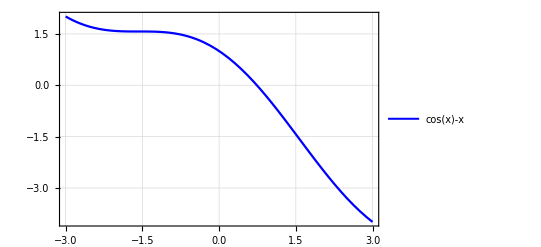

```mathematica
f[x_] :=Cos[x]-x
bisection[f,0,1,5]
```

## Question - 3

-10-x+x^4

1       1.75         2.

2       1.75         1.875

3       1.8125         1.875

4       1.84375         1.875

5       1.84375         1.85938

Root  = 1.85156

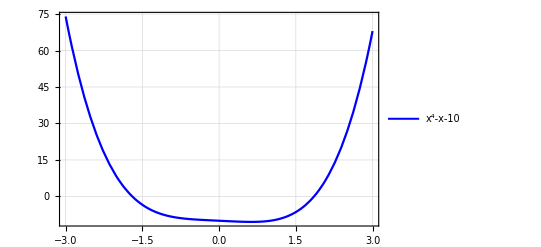

```mathematica
f[x_] = x^4-x-10
bisection[f,1.5,2,5]
```

## Question - 4

3 x^2 –

Bisection Method can not be applied !!

1       1.5         2.

2       1.75         2.

3       1.875         2.

4       1.9375         2.

5       1.96875         2.

Root  = 1.98438

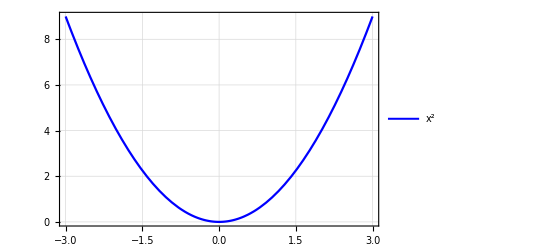

```mathematica
f[x_] =x^2–3
bisection[f,1,2,5]
```